```mathematica
(* ======================================================================================================================*)
(* Attempting to find some suitable analogue of the Multinomial Theorem when we lift the requirement that n, n_1,...,n_k be integers.*)
(* In fact, let's let n,n_1,...,n_k be positive real numbers where k is a positive integer.*) 
(* John H. Smith, johnhs3, 3-19-2022
(* ======================================================================================================================*)
```

```mathematica
(* DEFINITIONS: (from other project) *)
(*Generalized Binomial Coefficients -- y,x in R\Z_(<=-1) . I.e. for fixed y, we can think of genBinom as a function from R\Z_(<=-1) --> R *)
genBinom[y_,x_]:=Module[{y0=y,x0=x},Gamma[1+y0]/(Gamma[1+x0]*Gamma[1+y0-x0])]
(* Generalized Multinomial Coefficients -- n,n_1,...,n_k in R\Z_(<=-1). I.e. for fixed n, we can think of it as a function from (R\Z_(<=-1))^k --> R.  *)
genMultinom[n_,ni__]:=Module[{n0=n, args= ni},
(Gamma[n+1])/(Product[Gamma[i+1],{i,args}])
]
```

```mathematica
(* ======================================================================================================================*)
```

```mathematica
(* STAGE 1: Try simple Cases. *)
(* Trinomial. *)
(* =============== PARAMS =============== *)
xvec = {1,2,3};
r = Sqrt[2];
(* ====================================== *)
(* First, enumerate all the different sets of numbers that you're going to substitute into your sum. xvec = {x1,x2,x3}, nvec = {n1,n2,n3 = r-n1-n2}*)
argList = {{0,0,r},{0,1,r-1},{1,0,r-1}};
(* Next, perform the sum, summing over the list of arguments substituted into the appropriate variables. *)
result =0;
For[i=0,i<Length[argList],i++,
result+= genMultinom[r,{argList[[1,i]],argList[[2,i]],argList[[3,i]]}]*xvec[[1]]^argList[[1,i]]*xvec[[2]]^argList[[2,i]]*xvec[[3]]^argList[[3,i]];
Print["AAAA"]

]
N[result]
(* ======================================================================================================================*)
```

AAAA

AAAA

AAAA

6.26908+(1.25382 6.^List)/Gamma[1.+List]^3

```mathematica
(* ==================================== *)
N[(2+ 2+2)^(Sqrt[2])]
```

12.6029

```mathematica
N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*(2)^Sqrt[2],{n2,0,20}],{n1,0,20}]]
```

8.50541×10^6

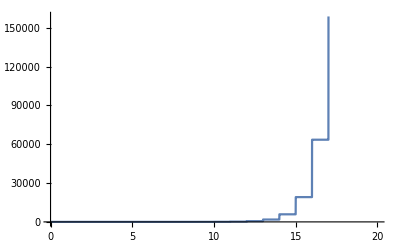

```mathematica
Plot[ N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*(2)^Sqrt[2],{n2,0,x}],{n1,0,x}]],{x,0,20}]
```

```mathematica
(* It blows up... not good. *)
(* Can we make a plot to visualize why? *)
Plot3D[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}],{n1,-10,10},{n2,-10,10}]
```

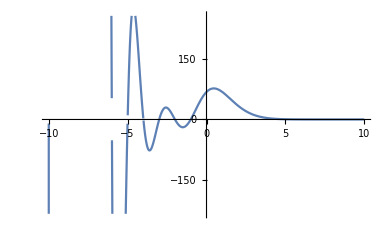

```mathematica
(* Why does it work for the 2 case? *)
Plot[genMultinom[Sqrt[2],{n1,Sqrt[2]-n}],{n1,-10,10}]
```

```mathematica
(* 4 case... *)
N[(8)^Sqrt[2]]
```

18.9305

```mathematica
N[Sum[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,n3,Sqrt[2]-n1-n2-n3}]*(2)^Sqrt[2],{n2,0,10}],{n1,0,10}],{n3,0,10}]]
```

6.43767×10^8

```mathematica
(* ============================================================================ *)
(* Now, what about when they're NOT equal??? Can we achieve convergence in this case? *)
N[(2+ Sqrt[2]+1)^(Sqrt[2])]
```

8.16508

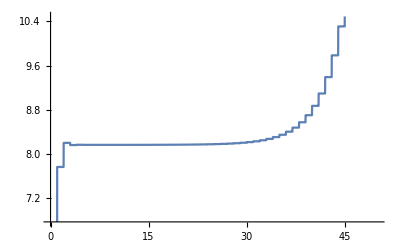

```mathematica
Plot[N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*2^(Sqrt[2]-n2-n1)*Sqrt[2]^n2*1^n1,{n2,0,x}],{n1,0,x}]],{x,0,50}]
```

```mathematica
(* Hmm... weird behavior. It seems to approximate the actual value quite well for the first 25 terms or so, then it blows up! Let's try some higher values with reorderings... *)
x=50;
N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*2^(Sqrt[2]-n2-n1)*Sqrt[2]^n2*1^n1,{n2,0,x}],{n1,0,x}]]
```

19.9827

```mathematica
(* Okay, from reordering a bunch of times I conclude that you should assign the (r-n1-n2) exponent to the LARGEST in magnitude of x1,x2,x3... *)
(* Now, let's investigate this plateau effect a bit more, by trying different numbers in both the x's and r's place... *)
N[(2+ Sqrt[2]+.5)^(Sqrt[2])]
```

6.88852

```mathematica
x=85;
N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*2^(Sqrt[2]-n2-n1)*Sqrt[2]^n2*.5^n1,{n2,0,x}],{n1,0,x}]]
```

General::munfl: 2.55179×10^-259 5.69864×10^-50 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.46746×10^-260 5.69864×10^-50 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.57518×10^-261 2.84932×10^-50 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

6.88852

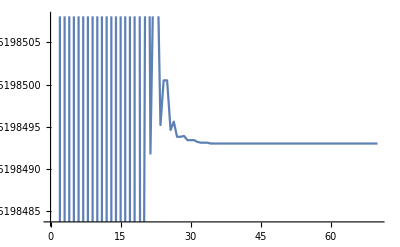

```mathematica
Plot[N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*2^(Sqrt[2]-n2-n1)*Sqrt[2]^n2*.5^n1,{n2,0,x}],{n1,0,x}]],{x,0,70}]
```

```mathematica
N[Sum[genBinom[Sqrt[2],n1]*2^(Sqrt[2]-n1)*(Sqrt[2]+1/2)^n1,{n1,0,x}]]
```

6.88852

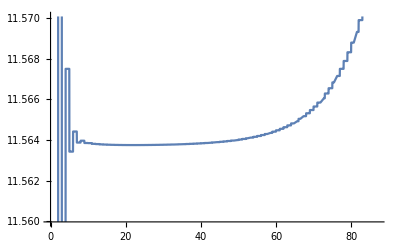

```mathematica
(* Plot: *)
Plot[N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*2^n2*Sqrt[7]^(Sqrt[2]-n2-n1)*1^n1,{n2,0,x}],{n1,0,x}]],{x,0,87}]
```

995.042

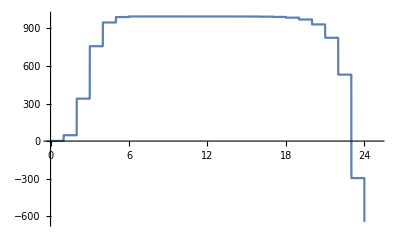

```mathematica
(* Later that night... (around 7 p.m. I spent a long time trying to prove a special case of the GMT based on the GBT, to no avail. o welll) *)
(* Sum over multinomials? At least now we can make a definitive conjecture, which can be proven true or false! *)
n = 2Pi;
k = 3;
N[k^n]

Plot[N[Sum[Sum[genMultinom[n,{n1,n2,n-n1-n2}],{n1,0,x}],{n2,0,x}]],{x,0,25}]
```

2.66514

7.10299

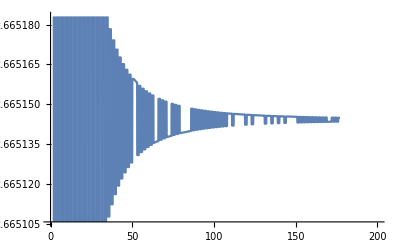

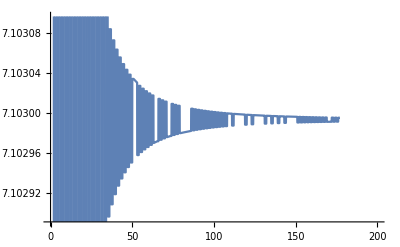

```mathematica
(* Okay, so this also approaches then diverges... *)
(* Made summary of conjectured behavior so far in my notes. *)


(* One last thing: Why doesn't the sum diverge for the k=2 case when |x|=|y| and r>0? *)
x=2;
y=2;
r=Sqrt[2];
N[2^Sqrt[2]]
N[(x+y)^r]
Plot[Sum[genMultinom[r,{n1,r-n1}],{n1,0,p}],{p,0,200}]
Plot[Sum[genMultinom[r,{n1,r-n1}]*x^n1*y^(r-n1),{n1,0,p}],{p,0,200}]
```

```mathematica
(* 3 - 22 - 2022 *)
(* Attempting to find a case that would disprove what I'm trying to show in the proof of GBT *)
z = 2 + 2I;
h =-1-I;
r = Sqrt[2];
N[(z+h)^r]
N[Sum[genBinom[r,k]*z^(r-k)*h^k,{k,0,Infinity}]]
```

0.724868+1.46278 ⅈ

0.724868+1.46278 ⅈ

```mathematica
N[(3Sqrt[2])^(3/2)]
```

8.73885

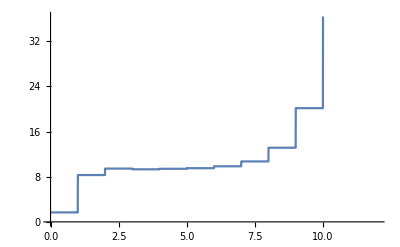

```mathematica
Plot[N[Sum[Sum[Gamma[3/2+1]/(Gamma[n1+1]*Gamma[n2+1]*Gamma[3/2-n1-n2+1])*(Sqrt[2])^n1*(Sqrt[2])^(3/2-n1-n2)*(Sqrt[2])^n1,{n2,0,x}],{n1,0,x}]],{x,0,12}]
```

```mathematica
(* Well, this means I have some proof checking to do... something I did in that exercise I just did was wrong, and perhaps that means that the limited case of the GMT that I proved the other day is wrong, too. I will check those at some point. *)

(* in the mean time, let's experiment and see what happens when we change our sum bounds... *)
(* Try: *)
```

```mathematica
n = 2Pi;
k = 3;
N[k^n]

Plot[N[Sum[Sum[genMultinom[n,{n1,n2,n-n1-n2}],{n1,0,x}],{n2,0,x}]],{x,0,25}]
```

995.042

-Graphics-

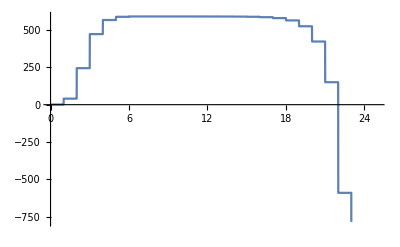

```mathematica
(* Now, reduce... *)
Plot[N[Sum[Sum[genMultinom[n,{n1,n2,n-n1-n2}],{n1,0,n2}],{n2,0,x}]],{x,0,25}]
```

```mathematica
(* Now it doesn't even hit the right value... fail. *)
(* A simpler case? *)
N[(2+ Sqrt[7]+1)^(Sqrt[2])]
```

11.5637

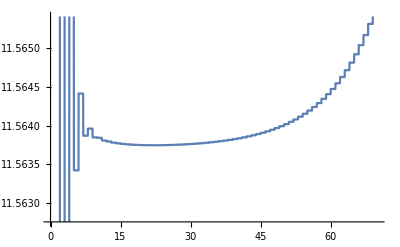

```mathematica
Plot[N[Sum[Sum[genMultinom[Sqrt[2],{n1,n2,Sqrt[2]-n1-n2}]*1^n2*Sqrt[7]^(Sqrt[2]-n2-n1)*2^n1,{n2,0,x}],{n1,0,x}]],{x,0,70}]
```

```mathematica
(0)^Sqrt[2]
```

0

```mathematica
Sum[genBinom[Sqrt[2],k]*0^(Sqrt[2]-k)*0^k,{k,0,Infinity}]
```

0

```mathematica
0^0
```

Power::indet: Indeterminate expression 0^0 encountered.

Indeterminate

```mathematica
r=Sqrt[2];
nvec = {-2,-1,-1/2};
n = Total[nvec];
N[n^r]
N[Norm[n^r]]
```

-1.56577-5.66841 ⅈ

5.88069

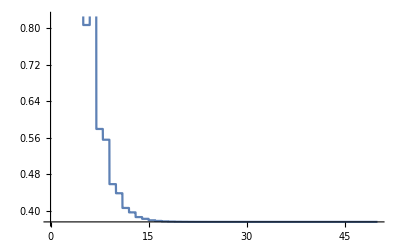

```mathematica
Plot[N[Norm[Sum[Sum[genMultinom[n,{n1,n2,n-n1-n2}]*(-2)^(r-n1-n2)*(-1)^n1*(-1/2)^n2,{n2,0,x}],{n1,0,x}]]],{x,0,50}]
```

```mathematica
N[Norm[Sum[Sum[genMultinom[n,{n1,n2,n-n1-n2}]*(-2)^(r-n1-n2)*(-1/2)^n1*(-1)^n2,{n2,0,90}],{n1,0,90}]]]
```

0.375913

```mathematica
NumberForm[4.103257835230283,16]
```

4.103257835230283